# Thesis

Litskevich Danila

## Описание

Кандида (гриб) – род дрожжей.

Мы берем модель с эпителиальными клетками x, растущими в системе с кандидозом y, которые подавляют рост эпителия, а рост кандиды, в свою очередь, подавляется бактерией стрептококков z.

## Модель I

Система дифференциальных уравнений имеет вид:

Piecewise[{{ⅆx/ⅆt=x(α-βy), }, {ⅆy/ⅆt=y(-γ+δx-ϵz), }, {ⅆz/ⅆt=z(-ϕ+ηy), }}]

α,β,γ,δ,ϵ,ϕ,η>0

## Безразмерный вид

Piecewise[{{ⅆx/ⅆt=x α(1-β/α y), }, {ⅆy/ⅆt=γ y(-1+δ/γ x-ϵ/γ z), }, {ⅆz/ⅆt=ϕ z(-1+η/ϕ y), }}]

Piecewise[{{X=δ/γ x, }, {Y=β/α y, }, {Z=ϵ/γ z, }, {τ=α t, }}]

Piecewise[{{ⅆX/ⅆτ=X (1-Y), }, {ⅆY/ⅆτ=γ/α Y(-1+X-Z), }, {ⅆZ/ⅆτ=ϕ/α Z(-1+η/ϕ α/β Y), }}]

Piecewise[{{ⅆX/ⅆτ=X (1-Y), }, {ⅆY/ⅆτ=a Y(-1+X-Z), }, {ⅆZ/ⅆτ=b Z(-1+c Y), }}]Piecewise[{{a=γ/α, }, {b=ϕ/α, }, {c=η/ϕ α/β, }}]a,b,c>0

## Положения равновесия (безразмерный вид)

Piecewise[{{ⅆx/ⅆt==0, }, {ⅆy/ⅆt==0, }, {ⅆz/ⅆt==0, }}]

Piecewise[{{X(1-Y)==0, }, {a Y(-1+X-Z)==0, }, {b Z(-1+c Y)==0, }}]

```mathematica
Solve[{X(1-Y)==0, Y(-1+X-Z)==0, Z(-1+c Y)==0},{X,Y,Z},Assumptions->{Z≥0}];
equilibriumPoints=%[[All,All,2]]
```

{{0,0,0},{1,1,0}}

### StreamPlot3D (v. 12.3+)

```mathematica
Manipulate[
Show[
StreamPlot3D[
{X(1-Y),a Y(-1+X-Z),b Z(-1+c Y)},
{X,0,1},{Y,0,1},{Z,0,1},
AxesLabel->{"x","y","z"},StreamMarkers->"Arrow"
],
Graphics3D[{PointSize[Medium],Red,Point[{{1,1,0},{0,0,0}}]},PlotRange->{{0,1},{0,1},{0,1}}
]
],
{a,Range[0.1,1,0.1],SetterBar},{b,Range[0.1,1,0.1],SetterBar},{c,2}]
```

```mathematica
Manipulate[
Show[
StreamPlot3D[
{X(1-Y),a Y(-1+X-Z),b Z(-1+c Y)},
{X,0.8,1.4},{Y,0.9,1.1},{Z,0,.1},
AxesLabel->{"x","y","z"},StreamMarkers->"Arrow",
StreamPoints->10
],
Graphics3D[{PointSize[Medium],Red,Point[{{1,1,0},{0,0,0}}]},PlotRange->{{0,1},{0,1},{0,1}}
]
],
{a,Range[0.1,1,0.1],SetterBar},{b,Range[0.1,1,0.1],SetterBar},{c,.92}]
```

### StreamPlot3D (одна спираль)

```mathematica
StreamPlot3D[
{X(1-Y), Y(-1+X-Z),Z(-1+0.9 Y)},
{X,0.8,1.4},{Y,0.9,1.1},{Z,0,.1},
AxesLabel->{"x","y","z"},StreamMarkers->"Arrow",
StreamPoints->{{1.1,1.1,0.1}},PlotLabel->Row[{"(x,y,z)=",{1.1,1.1,0.1}," c=",0.9}]
]
```

-Graphics3D-

-Graphics3D-

Цвет стрелок ведёт себя странно, но направлены в сторону уменьшения Z, а при Z=0, получается система Лотки-Вольтерра.

## StreamPlot2D

Piecewise[{{ⅆX/ⅆτ=X (1-Y), }, {ⅆY/ⅆτ=a Y(-1+X-Z), }, {ⅆZ/ⅆτ=b Z(-1+c Y), }}]Piecewise[{{a=γ/α, }, {b=ϕ/α, }, {c=η/ϕ α/β, }}]a,b,c>0

### X,Y

#### StreamPlot (x, y)

```mathematica
Manipulate[
StreamPlot[{X(1-Y),a Y(-1+X-Z)},{X,0.8,1.4},{Y,0.9,1.1},FrameLabel->{"x","y"}],
{{a,0.2},0.1,2,Appearance->"Labeled"},
{{Z,0.1},0,0.1,Appearance->"Labeled"}
]
```

При уменьшении Z до 0 “центр траекторий”  переходит в т. (1,1,0)

#### Траектория

Piecewise[{{ⅆX/ⅆτ=X (1-Y), }, {ⅆY/ⅆτ=a Y(-1+X-Z), }, {Z==const, }}]

ⅆX/(X (1-Y))=ⅆY/(a Y(-1+X-Z))

((-1+X-Z)ⅆX)/X=((1-Y)ⅆY)/(a Y)

X+(-1-Z) Log[X]=(-Y+Log[Y])/a

```mathematica
Manipulate[
ContourPlot[{X+(-1-Z) Log[X]-(-Y+Log[Y])/a},{X,0.8,1.4},{Y,0.9,1.1},FrameLabel->{"x","y"}],
{{a,0.2},0.1,2,Appearance->"Labeled"},
{{Z,0.1},0,0.1,Appearance->"Labeled"}
]
```

#### Линеаризация около (1+Z, 1)

Piecewise[{{ⅆX/ⅆτ=X (1-Y), }, {ⅆY/ⅆτ=a Y(-1+X-Z), }, {Z==const, }}]

Замена

Piecewise[{{x_1=X-(1+Z), }, {x_2=Y-1, }}]

Piecewise[{{(ⅆ x_1)/ⅆτ=-(x_1+1+Z) x_2, }, {(ⅆ x_2)/ⅆτ=a x_1(x_2+1), }, {Z==const, }}]

Piecewise[{{(ⅆ x_1)/ⅆτ≃-(1+Z) x_2, }, {(ⅆ x_2)/ⅆτ≃a x_1, }, {Z==const, }}]

A=(0 | -(1+Z)
a  | 0)

|A-E λ|=λ^2+a(1+Z)==0

λ_(1,2)=±ⅈ √(a(1+Z))

положение равновесия нейтрально устойчиво как в системе Лотки-Вольтерра

#### Вывод

Для любого  z_0 траектория для (x,y) – центр

### X,Z

#### StreamPlot (x,z)

```mathematica
Manipulate[
StreamPlot[{X(1-Y),b Z(-1+c Y)},{X,0.6,1.4},{Z,0,0.1},FrameLabel->{"x","z"}],
{{c,0.9},0.1,2,Appearance->"Labeled"},
{{b,0.2},0.1,2,Appearance->"Labeled"},
{{Y,0.98},0.9,1.1,Appearance->"Labeled"}
]
```

Z быстро сходится к 0 при c<1

#### Траектория

Piecewise[{{ⅆX/ⅆτ=X (1-Y), }, {Y=Const, }, {ⅆZ/ⅆτ=b Z(-1+c Y), }}]

ⅆX/(X (1-Y))=ⅆZ/(b Z(-1+c Y))

Log[X]/(1-Y)=Log[Z]/(b (-1+c Y))

X+(-1-Z) Log[X]=(-Y+Log[Y])/a

```mathematica
Manipulate[
ContourPlot[{Log[X]/(1-Y)-Log[Z]/(b (-1+c Y))},{X,0.8,1.4},{Z,0.001,0.1},FrameLabel->{"x","z"}],
{{c,0.9},0.1,2,Appearance->"Labeled"},
{{b,0.2},0.1,2,Appearance->"Labeled"},
{{Y,0.98},0.1,2,Appearance->"Labeled"}
]
```

#### Линеаризация около (1+Z, 1)

Piecewise[{{ⅆX/ⅆτ=X (1-Y), }, {Y=Const, }, {ⅆZ/ⅆτ=b Z(-1+c Y), }}]

Замена

Piecewise[{{x_1=X-(1+Z), }, {x_2=Y-1, }}]

Piecewise[{{(ⅆ x_1)/ⅆτ=-(x_1+1+Z) x_2, }, {(ⅆ x_2)/ⅆτ=a x_1(x_2+1), }, {Z==const, }}]

Piecewise[{{(ⅆ x_1)/ⅆτ≃-(1+Z) x_2, }, {(ⅆ x_2)/ⅆτ≃a x_1, }, {Z==const, }}]

A=(0 | -(1+Z)
a  | 0)

|A-E λ|=λ^2+a(1+Z)==0

λ_(1,2)=±ⅈ √(a(1+Z))

положение равновесия нейтрально устойчиво как в системе Лотки-Вольтерра

#### Вывод

Для любого  z_0 траектория для (x,y) – центр

### Y,Z

#### StreamPlot (y, z)

```mathematica
Manipulate[
StreamPlot[{ a Y(-1+X-Z),b Z(-1+0.9 Y)},{Y,0.5,1.5},{Z,0,0.3},StreamPoints->60,FrameLabel->{"y","z"}],
{{a,0.2},0.1,2,Appearance->"Labeled"},{{b,0.2},0.1,2,Appearance->"Labeled"},
{{X,1.06},0.8,1.4,Appearance->"Labeled"}
]
```

Предполагаю, что Z медленно сходится к 0 при c<1

Piecewise[{{ⅆY/ⅆτ=a Y(-1+X-Z), }, {ⅆZ/ⅆτ=b Z(-1+c Y), }}]Piecewise[{{a=γ/α, }, {b=ϕ/α, }, {c=η/ϕ α/β, }}]a,b,c,X>0

Положение равновесия  (1/c,X-1)

Piecewise[{{x_2=Y-1/c, }, {x_3=Z-(X-1), }}]

Piecewise[{{(ⅆ x_2)/ⅆτ=a (x_2+1/c)(-1+X-x_3-X+1), }, {(ⅆ x_3)/ⅆτ=b (x_3+X-1)(-1+c (x_2+1/c)), }}]Piecewise[{{(ⅆ x_2)/ⅆτ=a x_3(x_2+1/c), }, {(ⅆ x_3)/ⅆτ=b c x_2(x_3+(X-1)), }}]

A=(0 | a/c
b c (X-1)  | 0)

|A-E λ|==λ^2-a b (X-1)==0

λ_(1,2)=Piecewise[{{±√(a b (X-1)), X≤1 | □}, {±√(a b (1-X))ⅈ, X>1 | □}}]

## Линеаризация

Piecewise[{{ⅆX/ⅆτ=X (1-Y), }, {ⅆY/ⅆτ=a Y(-1+X-Z), }, {ⅆZ/ⅆτ=b Z(-1+c Y), }}]Piecewise[{{a=γ/α, }, {b=ϕ/α, }, {c=η/ϕ α/β, }}]a,b,c>0

### Около (0,0,0)

A=(1 | 0 | 0
0 | -a | 0
0 | 0 | -b)

λ_1=1    ⟹ Re λ_1 >0  ⟹ положение равновесия неустойчиво

### Около (1,1,0)

Замена

Piecewise[{{x_1=X-1, }, {x_2=Y-1, }, {x_3=Z, }}]

Piecewise[{{(ⅆ x_1)/ⅆτ=(x_1+1) (1-(x_2+1)), }, {(ⅆ x_2)/ⅆτ=a (x_2+1)(-1+x_1+1-x_3), }, {(ⅆ x_3)/ⅆτ=b x_3(-1+c (x_2+1)), }}]Piecewise[{{(ⅆ x_1)/ⅆτ=-x_2(x_1+1), }, {(ⅆ x_2)/ⅆτ=a (x_2+1)(x_1-x_3), }, {(ⅆ x_3)/ⅆτ=b x_3((c-1)+c x_2), }}]

A=(0 | -1 | 0
a  | 0 | -a 
0 | 0 | b(c-1))

|A-E λ|=(b(c-1)-λ)(λ^2+a)==0

λ_(1,2)=ⅈ √a

λ_3=b(c-1)

положение равновесия нейтрально устойчиво при c<1 (Re λ_3<1)

при z=0 система переходит в систему Лотки-Вольтерра

#### График

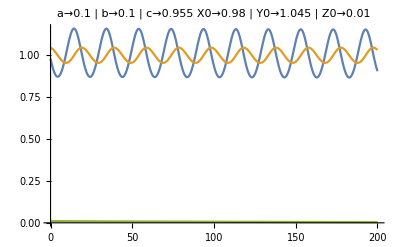

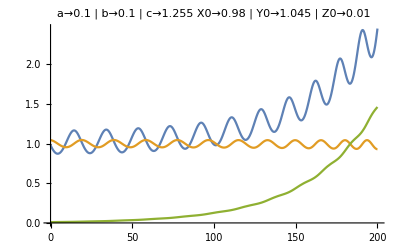

### Вывод

Система не имеет устойчивых положений равновесия

## Поглащающие положения равновесия

Piecewise[{{ⅆX/ⅆτ=X (1-Y), }, {ⅆY/ⅆτ=a Y(-1+X-Z), }, {ⅆZ/ⅆτ=b Z(-1+c Y), }}]Piecewise[{{a=γ/α, }, {b=ϕ/α, }, {c=η/ϕ α/β, }}]a,b,c>0

### Около (1,1,0)

Положение равновесия p_3=(1,1,0)

λ_3=b (-1+c Y)|_(1,1,0)=b(c-1)

при λ_3<0 положение равновесия будет поглащающим 
(т.е. орбита системы, поподающая в окрестность положения равновесия, стремится к положению равновесия)

Т.к. b>0,то условие c<1

### Вывод

Положение равновесия p_3=(1,1,0) – поглащающее

Следовательно, система не экологически устойчива

## Решение

```mathematica
ClearAll[X,Y,Z]
Manipulate[
With[{funcs=Association@@
NDSolve[{
D[X[t],t]==X[t](1-Y[t]),
D[Y[t],t]==a Y[t](-1+X[t]-Z[t]),
D[Z[t],t]==b Z[t](-1+c Y[t]),
X[0]==X0,
Y[0]==Y0,
Z[0]==Z0
},{X,Y,Z},{t,0,tmax}]},
GraphicsRow[{
Plot[
Evaluate@Through[Values[funcs][t]],{t,0,tmax},
PlotLabel->Grid[{
{"a"->a," b"->b," c"->c},
{"X0"->X0," Y0"->Y0," Z0"->Z0}
}],
PlotLegends->{"X","Y","Z"},PlotRange->{{0,tmax},All}],
Plot[
Evaluate@Values[funcs][[3]][t],{t,0,tmax},
PlotLegends->{"Z"},PlotRange->{{0,tmax},All}]
}]
],
{{a,0.2},0.1,2,Appearance->"Labeled"},{{b,0.2},0.1,2,Appearance->"Labeled"},{{c,0.92},0.1,4,Appearance->"Labeled"},
{{X0,0.98},0,2,Appearance->"Labeled"},{{Y0,1.045},0,2,Appearance->"Labeled"},{{Z0,0.3},0,2,Appearance->"Labeled"},
{tmax,40,Appearance->"Labeled"}
]
```

## Вывод

Система не имеет устойчивых положений равновесия.

Кроме того, в системе есть существенный недостаток: x растёт экспоненциально (модель Мальтуса) при отсутствии y и z 
О схожей проблеме говориться в главе 3.3 [1] для системы Лотки-Вольтерра.

В общем, если эту модель и можно применить к реальным данным, то только для короткого промежутка времени.

## Литература

Д. Мюррей. Математическая биология. Том I. Введение. -- М.-Ижевск, 2009.

## Модель II